# Mathematicaによる計量書誌学入門

## Mathematicaの基本

### インタープリタ

### 代入

変数への値の代入:

```mathematica
i=1
```

1

```mathematica
i
```

1

```mathematica
Set[j,2]
```

2

```mathematica
j
```

2

関数定義は”関数名+引数”のパターンに定義を代入する(正しくはパターンマッチと書き換えを定義している):

```mathematica
f[x_]:=x^2
```

```mathematica
f[4]
```

16

```mathematica
SetDelayed[g[x_],x^3]
```

```mathematica
g[4]
```

64

Nullの代入:

```mathematica
t=Null
```

```mathematica
t
```

```mathematica
{t}
```

{Null}

### 式の書き換え(項の置き換え)

書き換えルールの作成:

```mathematica
g->h
```

g→h

```mathematica
Rule[g,h]
```

g→h

ルールを適応して書き換え:

```mathematica
g[g[x]]
```

g[g[x]]

```mathematica
g[g[x]]/.g->h
```

h[h[x]]

```mathematica
ReplaceAll[g[g[x]],g->h]
```

h[h[x]]

```mathematica
f[g[g[x]]]/.g->h
```

f[h[h[x]]]

```mathematica
f[g][g[x]]/.g->h
```

f[h][h[x]]

評価してから置き換え:

```mathematica
{x,x,x}/.{x->Random[]}
```

{0.541974,0.541974,0.541974}

書き換えてから評価:

```mathematica
{x,x,x}/.{x:>Random[]}
```

{0.601004,0.891285,0.411149}

### 純関数

無名関数とも言う。

普通の関数定義:

```mathematica
f[x_,y_]:=x+y
```

純関数の定義:

```mathematica
Function[#1+#2](*定義のみ(再利用不可)、#1は1番目の引数、#2は2番目の引数*)
```

#1+#2&

```mathematica
Function[#1 + #2][1,2](*関数定義に直ちに引数を与えて使う*)
```

3

```mathematica
f=Function[#1 + #2](*定義を関数名に代入*)
```

#1+#2&

```mathematica
f[3,4]
```

7

```mathematica
Function[{x,y},x+y][1, 2](*引数には#でなく任意の名前を付けることができる*)
```

3

```mathematica
Function[Plus[##]][1,2,3]
(*##は引数すべてを参照する*)
```

6

Function[{x, y}, x + y][1, 2]のうちで、Function[{x,y},x+y]部分が頭部すなわち関数名となる。

```mathematica
Head[f[][][]]
```

f[][]

```mathematica
e[1]=Function[#1*#2]
```

#1 #2&

```mathematica
e[2]=Function[(#1*#2)^2]
```

(#1 #2)^2&

```mathematica
e[1][1, 2]
```

2

```mathematica
e[2][1, 2]
```

4

```mathematica
h[3,2]/.{h->Function[#1 #2]}(*一時的にhに関数を割り当てる*)
```

6

```mathematica
h[3,2]
```

h[3,2]

```mathematica
h[][3,2]/.{h[]->Function[#1 #2]}
```

6

```mathematica
h[][3,2]/.{h[]->Function[{x,y},x y]}
```

6

### 繰り返し

単純繰り返しも制御構文でなく関数 -> 処理が遅い 。

```mathematica
For[i=0,i<5,i++,i]
```

```mathematica
i
```

5

```mathematica
s=For[i=0,i<5,i++,i]
```

```mathematica
s
```

```mathematica
{s}
```

{Null}

繰り返しによる配列作成:

```mathematica
Table[i,{i,5}]
```

{1,2,3,4,5}

繰り返しによる配列作成 (多次元):

```mathematica
Table[i+j+k,{i,5},{j,4},{k,3}]
```

{{{3,4,5},{4,5,6},{5,6,7},{6,7,8}},{{4,5,6},{5,6,7},{6,7,8},{7,8,9}},{{5,6,7},{6,7,8},{7,8,9},{8,9,10}},{{6,7,8},{7,8,9},{8,9,10},{9,10,11}},{{7,8,9},{8,9,10},{9,10,11},{10,11,12}}}

繰り返しによる配列作成 (変数):

```mathematica
matc=Array[c,{2,3}]
```

{{c[1,1],c[1,2],c[1,3]},{c[2,1],c[2,2],c[2,3]}}

```mathematica
c[2,2]=5
```

5

```mathematica
matc
```

{{c[1,1],c[1,2],c[1,3]},{c[2,1],5,c[2,3]}}

```mathematica
d[3]=6
```

6

```mathematica
vecd=Array[d,5]
```

{d[1],d[2],6,d[4],d[5]}

関数の繰り返し適応:

```mathematica
Nest[Function[#+1],0,5]
```

5

```mathematica
Nest[#+1&,0,3]
```

3

```mathematica
NestList[Function[#+1],0,5]
```

{0,1,2,3,4,5}

### 条件分岐

条件分岐も制御構文でなく関数 -> 処理が遅い:

```mathematica
i=3
```

3

```mathematica
If[i<5,0,10]
```

0

```mathematica
Timing[Table[If[i<5,0,i],{i,10}]]
```

{0.,{0,0,0,0,5,6,7,8,9,10}}

```mathematica
Timing[Table[If[i<5,0,i],{i,100000}];]
```

{0.003999,Null}

項の置き換えを条件分岐のように使う ->さらに遅くなる:

```mathematica
i/.x_/;x<5->0
```

0

```mathematica
Timing[Table[i/.x_/;x<5->0,{i,10}]]
```

{0.,{0,0,0,0,5,6,7,8,9,10}}

```mathematica
Timing[Table[i/.x_/;x<5->0,{i,100000}];]
```

{0.357946,Null}

### 構造生成、構造処理(変換・変形)、構造テスト、構造アクセス

#### 構造の生成

```mathematica
t1=Table[{i,j},{i,3},{j,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}}}

```mathematica
Array[{##}&,{3,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}}}

```mathematica
Array[{##}&,{2,3,4}]
```

{{{{1,1,1},{1,1,2},{1,1,3},{1,1,4}},{{1,2,1},{1,2,2},{1,2,3},{1,2,4}},{{1,3,1},{1,3,2},{1,3,3},{1,3,4}}},{{{2,1,1},{2,1,2},{2,1,3},{2,1,4}},{{2,2,1},{2,2,2},{2,2,3},{2,2,4}},{{2,3,1},{2,3,2},{2,3,3},{2,3,4}}}}

```mathematica
tri= Table[{i,j},{i,5},{j,i}]
```

{{{1,1}},{{2,1},{2,2}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3},{4,4}},{{5,1},{5,2},{5,3},{5,4},{5,5}}}

```mathematica
tri//TableForm
```

1
1 |  |  |  | 
2
1 | 2
2 |  |  | 
3
1 | 3
2 | 3
3 |  | 
4
1 | 4
2 | 4
3 | 4
4 | 
5
1 | 5
2 | 5
3 | 5
4 | 5
5

#### 構造・表現の変換・変形

```mathematica
ft1=Map[f[#]&,t1]
```

{f[{{1,1},{1,2},{1,3},{1,4}}],f[{{2,1},{2,2},{2,3},{2,4}}],f[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Flatten[ft1/.f->List,{4}]
```

{{{{1,1,1,1}},{{2,2,2,2}},{{3,3,3,3}}},{{{1,2,3,4}},{{1,2,3,4}},{{1,2,3,4}}}}

```mathematica
Map[g,t1]
```

{g[{{1,1},{1,2},{1,3},{1,4}}],g[{{2,1},{2,2},{2,3},{2,4}}],g[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Map[g,t1,{1}]
```

{g[{{1,1},{1,2},{1,3},{1,4}}],g[{{2,1},{2,2},{2,3},{2,4}}],g[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Map[g,t1,{1}]
```

{g[{{1,1},{1,2},{1,3},{1,4}}],g[{{2,1},{2,2},{2,3},{2,4}}],g[{{3,1},{3,2},{3,3},{3,4}}]}

```mathematica
Map[g,ft1,{1}]//TableForm
```

g[f[{{1,1},{1,2},{1,3},{1,4}}]]
g[f[{{2,1},{2,2},{2,3},{2,4}}]]
g[f[{{3,1},{3,2},{3,3},{3,4}}]]

```mathematica
Apply[g,ft1,{1}]//TableForm
```

g[{{1,1},{1,2},{1,3},{1,4}}]
g[{{2,1},{2,2},{2,3},{2,4}}]
g[{{3,1},{3,2},{3,3},{3,4}}]

ApplyとMapの違い

```mathematica
Map[f[#]&,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
Map[f[#]&,{1,2,3},{0}]
```

f[{1,2,3}]

```mathematica
Apply[f,{1,2,3}]
```

f[1,2,3]

```mathematica
Apply[Plus,{1,2,3}]
```

6

```mathematica
Map[Plus,{1,2,3}]
```

{1,2,3}

外積

```mathematica
Outer[List,{1,2,3},{4,5,6}]
```

{{{1,4},{1,5},{1,6}},{{2,4},{2,5},{2,6}},{{3,4},{3,5},{3,6}}}

```mathematica
tft1=Outer[List,t1,ft1]
```

{{{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{4,f[{{1,1},{1,2},{1,3},{1,4}}]},{4,f[{{2,1},{2,2},{2,3},{2,4}}]},{4,f[{{3,1},{3,2},{3,3},{3,4}}]}}}},{{{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{4,f[{{1,1},{1,2},{1,3},{1,4}}]},{4,f[{{2,1},{2,2},{2,3},{2,4}}]},{4,f[{{3,1},{3,2},{3,3},{3,4}}]}}}},{{{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{4,f[{{1,1},{1,2},{1,3},{1,4}}]},{4,f[{{2,1},{2,2},{2,3},{2,4}}]},{4,f[{{3,1},{3,2},{3,3},{3,4}}]}}}}}

内積

```mathematica
Inner[List,{1,2,3},{4,5,6},List]
```

{{1,4},{2,5},{3,6}}

```mathematica
Inner[Times,{1,2,3},{4,5,6},List]
```

{4,10,18}

```mathematica
Inner[Times,{1,2,3},{4,5,6},Plus]
```

32

```mathematica
tft1I=Inner[List,t1,ft1,List,1]
```

{{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{1,f[{{2,1},{2,2},{2,3},{2,4}}]},{1,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{2,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{2,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{3,f[{{1,1},{1,2},{1,3},{1,4}}]},{3,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}}},{{{1,f[{{1,1},{1,2},{1,3},{1,4}}]},{2,f[{{2,1},{2,2},{2,3},{2,4}}]},{3,f[{{3,1},{3,2},{3,3},{3,4}}]}},{{4,f[{{1,1},{1,2},{1,3},{1,4}}]},{4,f[{{2,1},{2,2},{2,3},{2,4}}]},{4,f[{{3,1},{3,2},{3,3},{3,4}}]}}}}

```mathematica
tft1C=Inner[Times,t1,ft1,Tr,1]
```

{{Tr[f[{{1,1},{1,2},{1,3},{1,4}}],2 f[{{2,1},{2,2},{2,3},{2,4}}],3 f[{{3,1},{3,2},{3,3},{3,4}}]],Tr[f[{{1,1},{1,2},{1,3},{1,4}}],f[{{2,1},{2,2},{2,3},{2,4}}],f[{{3,1},{3,2},{3,3},{3,4}}]]},{Tr[f[{{1,1},{1,2},{1,3},{1,4}}],2 f[{{2,1},{2,2},{2,3},{2,4}}],3 f[{{3,1},{3,2},{3,3},{3,4}}]],Tr[2 f[{{1,1},{1,2},{1,3},{1,4}}],2 f[{{2,1},{2,2},{2,3},{2,4}}],2 f[{{3,1},{3,2},{3,3},{3,4}}]]},{Tr[f[{{1,1},{1,2},{1,3},{1,4}}],2 f[{{2,1},{2,2},{2,3},{2,4}}],3 f[{{3,1},{3,2},{3,3},{3,4}}]],Tr[3 f[{{1,1},{1,2},{1,3},{1,4}}],3 f[{{2,1},{2,2},{2,3},{2,4}}],3 f[{{3,1},{3,2},{3,3},{3,4}}]]},{Tr[f[{{1,1},{1,2},{1,3},{1,4}}],2 f[{{2,1},{2,2},{2,3},{2,4}}],3 f[{{3,1},{3,2},{3,3},{3,4}}]],Tr[4 f[{{1,1},{1,2},{1,3},{1,4}}],4 f[{{2,1},{2,2},{2,3},{2,4}}],4 f[{{3,1},{3,2},{3,3},{3,4}}]]}}

Mathematicaの数式をリスト(ツリー)に展開する

```mathematica
x^2-x-2
```

-2-x+x^2

```mathematica
FullForm[x^2-x-2]
```

Plus[-2,Times[-1,x],Power[x,2]]

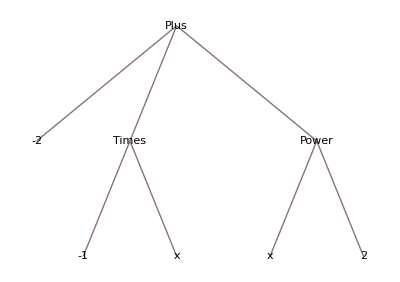

```mathematica
TreeForm[x^2-x-2]
```

#### 構造のテスト

```mathematica
Dimensions[t1]
```

{3,4,2}

```mathematica
Dimensions[Map[g,t1]]
```

{3}

```mathematica
Dimensions[Map[g,t1,{-1}]]
```

{3,4,2}

```mathematica
Dimensions[tft1]
```

{3,4,2,3,2}

```mathematica
Depth[tft1]
```

9

Depth[]はテンソルのランク+1を返す。あるいは、ツリーの深さを返す。

```mathematica
Depth[123]
```

1

TensorRank[]も使える。

```mathematica
TensorRank[{{2,1},{3,4}}]
```

2

```mathematica
TensorRank[{{2,1,{2}},{3,4,{2}}}]
```

2

```mathematica
Dimensions[tft1]
```

{4,2,3,2}

```mathematica
Dimensions[tft1I]
```

{4,2,3,2}

```mathematica
Dimensions[tft1C]
```

{4,2}

#### 構造へのアクセス

高次元データへのアクセス:

```mathematica
tft1C[[1,1,1,1]]
```

{{1,1},{1,2},{1,3},{1,4}}

変数に格納された構造の一部を直接参照して置き換え可能:

```mathematica
tft1C[[1,1,1,1]]=10
```

10

```mathematica
tft1C
```

{{f[10]+2 f[{{2,1},{2,2},{2,3},{2,4}}]+3 f[{{3,1},{3,2},{3,3},{3,4}}],f[{{1,1},{1,2},{1,3},{1,4}}]+f[{{2,1},{2,2},{2,3},{2,4}}]+f[{{3,1},{3,2},{3,3},{3,4}}]},{f[{{1,1},{1,2},{1,3},{1,4}}]+2 f[{{2,1},{2,2},{2,3},{2,4}}]+3 f[{{3,1},{3,2},{3,3},{3,4}}],2 f[{{1,1},{1,2},{1,3},{1,4}}]+2 f[{{2,1},{2,2},{2,3},{2,4}}]+2 f[{{3,1},{3,2},{3,3},{3,4}}]},{f[{{1,1},{1,2},{1,3},{1,4}}]+2 f[{{2,1},{2,2},{2,3},{2,4}}]+3 f[{{3,1},{3,2},{3,3},{3,4}}],3 f[{{1,1},{1,2},{1,3},{1,4}}]+3 f[{{2,1},{2,2},{2,3},{2,4}}]+3 f[{{3,1},{3,2},{3,3},{3,4}}]},{f[{{1,1},{1,2},{1,3},{1,4}}]+2 f[{{2,1},{2,2},{2,3},{2,4}}]+3 f[{{3,1},{3,2},{3,3},{3,4}}],4 f[{{1,1},{1,2},{1,3},{1,4}}]+4 f[{{2,1},{2,2},{2,3},{2,4}}]+4 f[{{3,1},{3,2},{3,3},{3,4}}]}}

ただし、関数が引数として受け取った構造に対しての書き換えは禁止されている(コピーされた構造を書き換えたものを返す):

```mathematica
l2={1,2,3}
```

{1,2,3}

```mathematica
ReplacePart[l2,{1}->10]
```

{10,2,3}

```mathematica
l2
```

{1,2,3}

一旦評価してもとの変数に代入:

```mathematica
l2=ReplacePart[l2,{1}->10]
```

{10,2,3}

```mathematica
l2
```

{10,2,3}

### 微分記号 ‘ (ダッシュ)と微分関数D

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
j[x_]:=x^3
```

```mathematica
j' (*j'そのものが関数として使える*)
```

3 #1^2&

```mathematica
FullForm[j']
```

Function[Times[3,Power[Slot[1],2]]]

```mathematica
j'[g]
```

3 g^2

```mathematica
Derivative[1][j][g]
```

3 g^2

Derivativeを使って直接微分する:

```mathematica
Derivative[1][x^3][x] (*jの代わりにx^3では微分しない -> 関数として定義されている必要がある*)
```

(x^3)'[x]

```mathematica
Derivative[1][x^3](*x^3 という関数名として認識される*)
```

(x^3)'

```mathematica
Function[u, u^3][x]
```

x^3

```mathematica
Derivative[1][Function[u,u^3]][x](*そこで、純関数を使う*)
```

3 x^2

```mathematica
Derivative[1][Function[u,j[u]]][x]
```

3 x^2

```mathematica
Derivative[1][Function[x,x^3]][x]
```

3 x^2

Dを使って直接微分する

```mathematica
D[x^3,x]
```

3 x^2

### 局所変数

```mathematica
h[x_]:=Module[{a},
a=2;
x^a
]
```

```mathematica
h[5]
```

25

```mathematica
a
```

a

### Mathematicaの式・データ構造

Mathematicaの場合、式はリストであり、頭部の情報にデータ型を含む。関数Head[]によって返されるオブジェクトである。関数にHead[]を適応すると、返される値は関数名である。

```mathematica
Head[a]
```

Symbol

```mathematica
Head[6]
```

Integer

```mathematica
Head[6.]
```

Real

```mathematica
Head[1-I]
```

Complex

```mathematica
Head["AAA"]
```

String

```mathematica
Head[fib]
```

Symbol

Headをネストさせて作用させると最終的にSymbolが得られる

```mathematica
Head[f[][][]]
```

f[][]

```mathematica
Head[f[][][]]//Head
```

f[]

```mathematica
Head[f[][][]]//Head//Head
```

f

```mathematica
Head[f[][][]]//Head//Head//Head
```

Symbol

```mathematica
Head[f[][][]]//Head//Head//Head//Head
```

Symbol

```mathematica
Head[6]//Head
```

Symbol

#### リスト(Mathematicaではリストもツリーで表される)

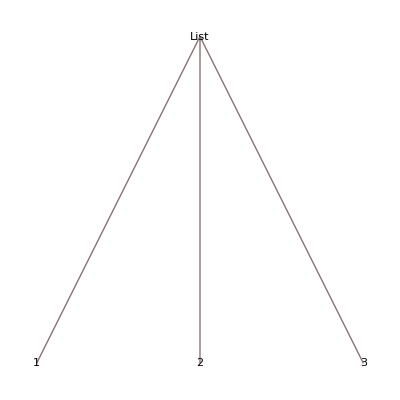

```mathematica
TreeForm[{1,2,3}]
```

#### ツリー

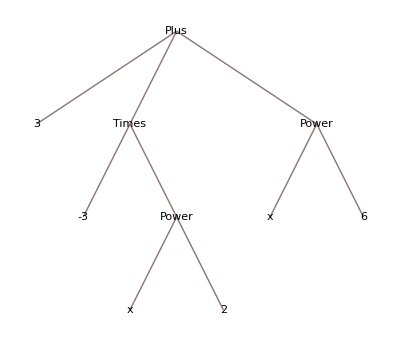

```mathematica
TreeForm[x^6-3x^2+3]
```

```mathematica
TreeForm[7^6-7*8+2]
```

-Graphics-

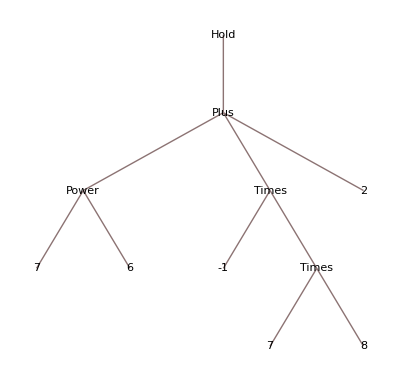

```mathematica
TreeForm[Hold[7^6-7*8+2]]
```

#### グラフ

リストでグラフは直接表現できないので、 Graph[]という予約済み関数を使う。

```mathematica
??Graph
```

RowBox[{"Graph", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] 辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{StyleBox["{", "TI"], RowBox[{StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], "TI"], ",", StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], "TI"], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}], ",", RowBox[{StyleBox["{", "TI"], RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}]}], "]"}] 頂点 SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]]，辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["j", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 頂点と辺の特性が記号ラッパー SubscriptBox[StyleBox["w", "TI"], StyleBox["k", "TI"]]で定義されているグラフを与える．

Attributes[Graph]={NHoldAll,Protected}
 
Options[Graph]={AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSelectable→Automatic,DirectedEdges→Automatic,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→Automatic,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,Epilog→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,Prolog→{},Properties→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{},VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→Automatic,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic}

#### 配列

Mathematicaにおいて、配列はリストの入れ子と変わりない。

1次元配列:

```mathematica
Table[x,{x,5}]
```

{1,2,3,4,5}

2次元配列:

```mathematica
Table[{x,y},{x,5},{y,5}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5}},{{2,1},{2,2},{2,3},{2,4},{2,5}},{{3,1},{3,2},{3,3},{3,4},{3,5}},{{4,1},{4,2},{4,3},{4,4},{4,5}},{{5,1},{5,2},{5,3},{5,4},{5,5}}}

3次元配列:

```mathematica
Table[{x,y,z},{x,5},{y,5},{z,5}]
```

{{{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5}},{{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5}},{{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5}},{{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5}},{{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5}}},{{{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5}},{{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5}},{{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5}},{{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5}},{{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5}}},{{{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5}},{{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5}},{{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5}},{{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5}},{{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5}}},{{{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5}},{{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5}},{{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5}},{{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5}},{{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5}}},{{{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5}},{{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5}},{{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5}},{{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5}},{{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5}}}}

#### 構造体

Mathematicaに構造体はない。かわりにリストを入れ子(ツリー)にして表現する。

```mathematica
x={1,2,2,{1,2,{1}}}
```

{1,2,2,{1,2,{1}}}

```mathematica
x
```

{1,2,2,{1,2,{1}}}

#### ポインタ

Mathematicaでのポインタは単に変数となる。

従って、変数に対し再帰定義もできる。

```mathematica
y=.
y={1,2,y}
```

$RecursionLimit::reclim: 最大再帰回数1024を超えています．

{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{MaxFormatDepthExceeded}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

ちゃんと、yには再帰構造が定義されている。

```mathematica
y
```

$RecursionLimit::reclim: 最大再帰回数1024を超えています．

{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{MaxFormatDepthExceeded}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

## 書誌データ

### データの尺度水準

定性値

名義尺度
値は、命名、分類のために用いられる。
要素の数え上げが可能。
集合 ?

順序尺度
値は、序列、順序を示す。
数え上げ + 序列に関する統計的扱いが可能となる。
位相 ?

定量値

間隔尺度
間隔に意味があるが、原点がない。
数え上げ + 序列に関する統計的扱い + 足し算引き算が可能。
加算に対して閉じている系(群ともちょっと違う) ?

比率尺度
原点からの距離を表す。
数え上げ + 序列に関する統計的扱い + 足し算引き算 + 掛け算割り算が可能。
環・体 ?

### 書誌データ

## 成長曲線

## 生産性の分布

### 正規分布

### 二項分布

### Zipf族分布

## 引用分析

## 文書クラスタリング

## ランキング

## 関係性データベース・検索

## 他分野との関連

### 計量言語学

### ケモメトリクス

### バイオインフォマティクス